{{1.,0.95238,0.},{0.5,1.00605,0.00165}}

{{1.,0.38133,0.000230723},{0.5,0.418117,0.000899932}}

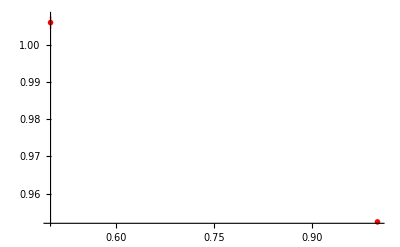

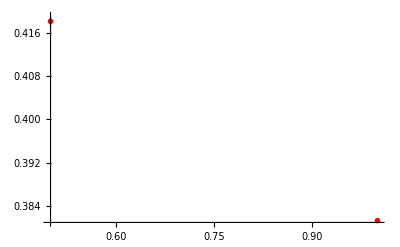

```mathematica
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
SUNData=GetConvergenceData["G:\\LAT\\sd_metropolis\\data\\sc_sm\\scalars_d1_t2_s1_l4.0000_rsm.dat",1,2,0.0,1.0,10]
LinkData=GetConvergenceData["G:\\LAT\\sd_metropolis\\data\\sc_sm\\scalars_d1_t2_s1_l4.0000_rsm.dat",1,4,0.0,1.0,10]
PlotWithErrors[SUNData,Red]
PlotWithErrors[LinkData,Red]
```

```mathematica
N[1/4+1/32]
```

0.28125